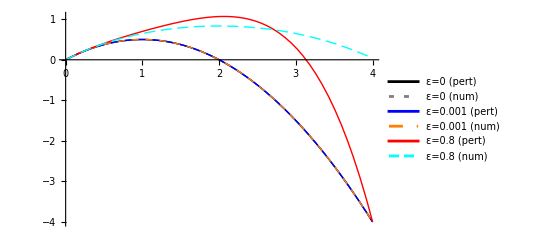

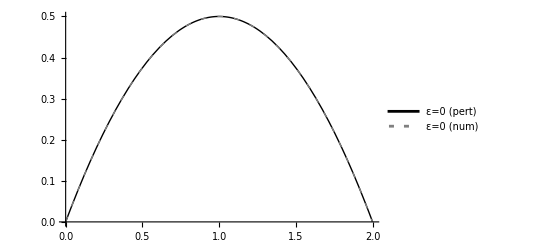

```mathematica
Clear[y,yNum,τ,ε]
y[τ_,ε_]:=τ-τ^2/2+ε*(τ^3/3-τ^4/12);
sol[ε_]:=NDSolve[{yNum''[τ]==-1/(1+ε yNum[τ])^2,yNum[0]==0,yNum'[0]==1},yNum,{τ,0,2}];
Plot[{y[τ,0],Evaluate[yNum[τ]/. sol[0]],y[τ,0.001],Evaluate[yNum[τ]/. sol[0.001]],y[τ,0.8],Evaluate[yNum[τ]/. sol[0.8]]},{τ,0,4},PlotStyle->{{Black,Thick},{Gray,Thick,Dashing[{0.01,0.02}]},{Blue,Thick},{Orange,Thick,Dashed},{Red,Thick},{Cyan,Thick,Dashing[{0.02,0.01}]}   },
PlotLegends->{"ε=0 (pert)","ε=0 (num)","ε=0.001 (pert)","ε=0.001 (num)","ε=0.8 (pert)","ε=0.8 (num)"}]

(*对比 ε = 0 的情况*)
Plot[{y[τ,0],Evaluate[yNum[τ]/. sol[0]]},{τ,0,2},PlotStyle->{{Black,Thick},{Gray,Thick,Dashing[{0.01,0.02}]}   },PlotLegends->{"ε=0 (pert)","ε=0 (num)"}]
(*对比 ε = 0 在末端的区别*)
Plot[{y[τ,0.001],y[τ,0]},{τ,1.99,2.01},PlotStyle->{{Black,Thick},{Gray,Thick,Dashing[{0.01,0.02}]}   },PlotLegends->{"ε=0.001 (pert)","ε=0 (pert)"}]
```

```mathematica
Clear[τ,ε,T1,T2]

(*定义 y*)
y[τ_]:=τ-τ^2/2+ε*(τ^3/3-τ^4/12);

(*代入 T=T0+ε T1*)
expr=Expand[y[2+ε T1 + ε^2T2]];


(*按 ε 展开到一阶*)
series=Series[expr,{ε,0,2}]//Normal

(*提取各阶系数*)
eq0=Coefficient[series,ε,1]==0;
eq1=Coefficient[series,ε,2]==0;

(*解方程*)
Solve[{eq0,eq1},{T1,T2}]
```

(4/3-T1) ε+((4 T1)/3-T1^2/2-T2) ε^2

{{T1→4/3,T2→8/9}}